# Windy Postman Problem

Peter Cullen Burbery

Abstract

## Section

XXXX:

## Optimization Formulation

## Example Graph

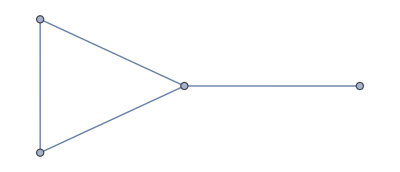

```mathematica
g
```

```mathematica
Clear[g]
```

```mathematica
UnbalancedMixedWeightedGraph=Graph[{Annotation[b<->c,EdgeWeight->2],Annotation[c<->d,EdgeWeight->3],Annotation[d->e,EdgeWeight->5],Annotation[e<->f,EdgeWeight->7],Annotation[f->b,EdgeWeight->11],Annotation[g->b,EdgeWeight->19],Annotation[g<->d,EdgeWeight->17],Annotation[d->b,EdgeWeight->13]},EdgeLabels->"EdgeWeight",VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding",PlotTheme->"Classic"]
```

-Graphics-

```mathematica
EdgeList[UnbalancedMixedWeightedGraph]
```

{b<->c,c<->d,d->e,e<->f,f->b,g->b,g<->d,d->b}

```mathematica
EdgeList[UnbalancedMixedWeightedGraph,b<->_]
```

{b<->c,f->b,g->b,d->b}

```mathematica
VertexComponent[UnbalancedMixedWeightedGraph,b]
```

{b,f,g,d,c,e}

```mathematica
VertexComponent[UnbalancedMixedWeightedGraph,c]
```

{c,b,d,f,g,e}

```mathematica
VertexComponent[UnbalancedMixedWeightedGraph,d]
```

{d,c,g,b,f,e}

```mathematica
VertexComponent[UnbalancedMixedWeightedGraph,e]
```

{e,d,f,c,g,b}

```mathematica
VertexComponent[UnbalancedMixedWeightedGraph,f]
```

{f,e,d,c,g,b}

```mathematica
VertexComponent[UnbalancedMixedWeightedGraph,g]
```

{g,d,c,b,f,e}

```mathematica
UnbalanceList[UnbalancedMixedWeightedGraph,b]
```

{{},{f->b,g->b,d->b},{b<->c}}

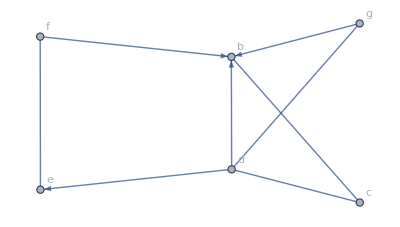

```mathematica
GraphDifference[UnbalancedMixedWeightedGraph,Graph[{b},{}],VertexLabels->Automatic]
```

```mathematica
Graph[UnbalancedMixedWeightedGraph,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
EdgeList[UnbalancedMixedWeightedGraph,(*arcs entering S={b,c,d}*)_->(b|c|d)]
```

{f->b,g->b,d->b}

We need to filter out d->b because d is still in the set:

```mathematica
EdgeList[UnbalancedMixedWeightedGraph,(*arcs entering S={b,c,d}*)Except[(b|c|d)]->(b|c|d)]
```

{f->b,g->b}

```mathematica
EdgeList[UnbalancedMixedWeightedGraph,(*arcs leaving S={b,c,d}*)(b|c|d)->Except[(b|c|d)]]
```

{d->e}

```mathematica
FindEdgeCut[UnbalancedMixedWeightedGraph]
```

{b<->c,d->e,g->b,d->b}

```mathematica
FindMinimumCut[UnbalancedMixedWeightedGraph]
```

{2,{{b,e,f},{c,d,g}}}

```mathematica
HighlightGraph[UnbalancedMixedWeightedGraph,FindEdgeCut[UnbalancedMixedWeightedGraph]]
```

-Graphics-

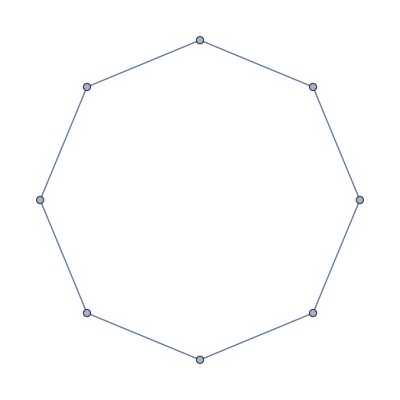

```mathematica
CycleGraph[8]
```

```mathematica
FindEdgeCut[CycleGraph[8]]
```

{1<->8,7<->8}

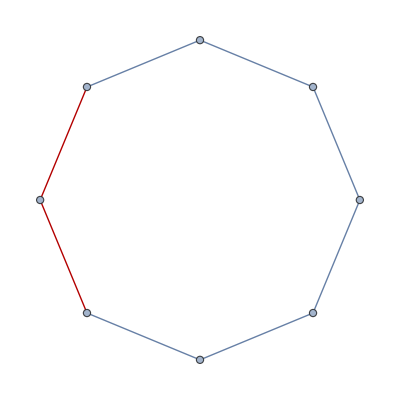

```mathematica
HighlightGraph[CycleGraph[8],FindEdgeCut[CycleGraph[8]]]
```

```mathematica
Names["*Cut"]
```

{FindEdgeCut,FindMaximumCut,FindMinimumCut,FindVertexCut}

```mathematica
Information/@Names["*Cut"]
```

{,,,}

```mathematica
FindEdgeCut[UnbalancedMixedWeightedGraph]
```

{b<->c,d->e,g->b,d->b}

```mathematica
EdgeDelete[UnbalancedMixedWeightedGraph,FindEdgeCut[UnbalancedMixedWeightedGraph]]
```

-Graphics-

```mathematica
Names["*MatrixDistribution"]
```

{CircularOrthogonalMatrixDistribution,CircularQuaternionMatrixDistribution,CircularRealMatrixDistribution,CircularSymplecticMatrixDistribution,CircularUnitaryMatrixDistribution,GaussianOrthogonalMatrixDistribution,GaussianSymplecticMatrixDistribution,GaussianUnitaryMatrixDistribution,InverseWishartMatrixDistribution,WishartMatrixDistribution}

```mathematica
ConvexOptimization[x,({{1, 2}, {2, 4}}).x<=({{3}, {5}}),{x}]
```

ConvexOptimization[x,{{1,2},{2,4}}.x≤{{3},{5}},{x}]

```mathematica
undirectedGraph=UndirectedGraph[UnbalancedMixedWeightedGraph]
```

-Graphics-

```mathematica
EulerianGraphQ[undirectedGraph]
```

True

```mathematica
FindPostmanTour[undirectedGraph]
```

{{b<->f,f<->e,e<->d,d<->b,b<->g,g<->d,d<->c,c<->b}}

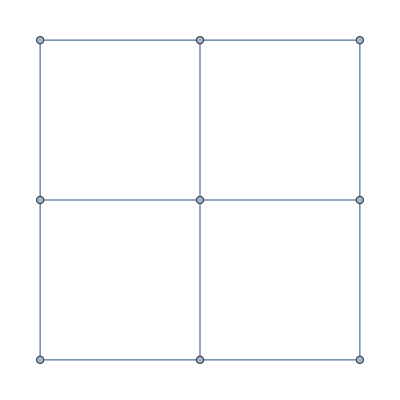

```mathematica
undirectedGraph=GridGraph[{3,3}]
```

```mathematica
EulerianGraphQ[undirectedGraph]
```

False

```mathematica
FindPostmanTour[undirectedGraph]
```

{{1<->4,4<->7,7<->8,8<->9,9<->6,6<->9,9<->8,8<->5,5<->6,6<->3,3<->2,2<->5,5<->4,4<->1,1<->2,2<->1}}

```mathematica
FindEdgeCut[undirectedGraph]
```

{6<->9,8<->9}

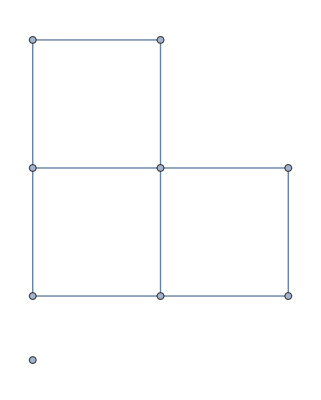

```mathematica
EdgeDelete[undirectedGraph,FindEdgeCut[undirectedGraph]]
```

```mathematica
EdgeAdd[undirectedGraph,First@FindPostmanTour[undirectedGraph]]
```

-Graphics-

```mathematica
Graph[First@FindPostmanTour[undirectedGraph]]
```

-Graphics-

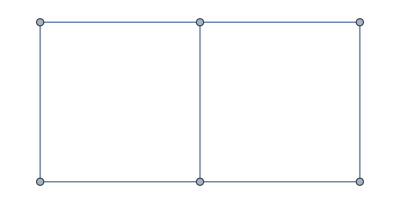

```mathematica
GridGraph[{2,3}]
```

```mathematica
EdgeList[GridGraph[{3,3}]]
```

{1<->2,1<->4,2<->3,2<->5,3<->6,4<->5,4<->7,5<->6,5<->8,6<->9,7<->8,8<->9}

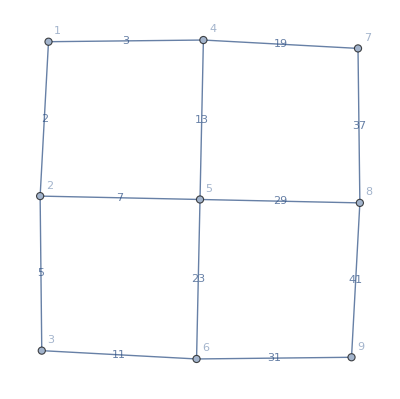

```mathematica
weightedUndirectedGraph=Graph[{Annotation[1<->2,EdgeWeight->2],Annotation[1<->4,EdgeWeight->3],Annotation[2<->3,EdgeWeight->5],Annotation[2<->5,EdgeWeight->7],Annotation[3<->6,EdgeWeight->11],Annotation[4<->5,EdgeWeight->13],Annotation[4<->7,EdgeWeight->19],Annotation[5<->6,EdgeWeight->23],Annotation[5<->8,EdgeWeight->29],Annotation[6<->9,EdgeWeight->31],Annotation[7<->8,EdgeWeight->37],Annotation[8<->9,EdgeWeight->41]},VertexLabels->Automatic,EdgeLabels->"EdgeWeight"]
```

```mathematica
FindPostmanTour[weightedUndirectedGraph]
```

{{1<->4,4<->7,7<->8,8<->5,5<->8,8<->9,9<->6,6<->5,5<->6,6<->3,3<->2,2<->5,5<->4,4<->1,1<->2,2<->1}}

```mathematica
Graph[First[FindPostmanTour[weightedUndirectedGraph]]]
```

-Graphics-

```mathematica
EdgeAugmentationVariables=
```

```mathematica
Graph[{Annotation[1->3,EdgeWeight->5],Annotation[3->1,EdgeWeight->4],Annotation[1->3,EdgeWeight->6],Annotation[3->2,EdgeWeight->3],Annotation[2->3,EdgeWeight->3],Annotation[2->3,EdgeWeight->2],Annotation[2->1,EdgeWeight->1],Annotation[1->2,EdgeWeight->1]}]
```

-Graphics-

```mathematica
EulerianGraphQ[Graph[{Annotation[1->3,EdgeWeight->5],Annotation[3->1,EdgeWeight->4],Annotation[1->3,EdgeWeight->6],Annotation[3->2,EdgeWeight->3],Annotation[2->3,EdgeWeight->3],Annotation[2->3,EdgeWeight->2],Annotation[2->1,EdgeWeight->1],Annotation[1->2,EdgeWeight->1]}]]
```

False

```mathematica
FindShortestPath[Graph[{1, 3, 2}, {DirectedEdge[1, 3], DirectedEdge[3, 1], DirectedEdge[1, 3], DirectedEdge[3, 2], DirectedEdge[2, 3], DirectedEdge[2, 3], DirectedEdge[2, 1], DirectedEdge[1, 2]}, {EdgeWeight -> {6, 4, 6, 3, 2, 2, 1, 1}}],All,All]
```

ShortestPathFunction[{All,All},«»]

```mathematica
FindHamiltonianCycle[Graph[{1, 3, 2}, {DirectedEdge[1, 3], DirectedEdge[3, 1], DirectedEdge[1, 3], DirectedEdge[3, 2], DirectedEdge[2, 3], DirectedEdge[2, 3], DirectedEdge[2, 1], DirectedEdge[1, 2]}, {EdgeWeight -> {6, 4, 6, 3, 2, 2, 1, 1}}]]
```

{{1->3,3->2,2->1}}

```mathematica
FindShortestTour[Graph[{Annotation[1->3,EdgeWeight->5],Annotation[3->1,EdgeWeight->4],Annotation[1->3,EdgeWeight->6],Annotation[3->2,EdgeWeight->3],Annotation[2->3,EdgeWeight->3],Annotation[2->3,EdgeWeight->2],Annotation[2->1,EdgeWeight->1],Annotation[1->2,EdgeWeight->1]}]]
```

FindShortestTour[-Graphics-]

## NP Complete Problems

```mathematica
Names["*Find*Tree*"]
```

{FindSpanningTree}

```mathematica
Names["*Clique*"]
```

{FindClique,FindKClique}

```mathematica
?FindClique
```

```mathematica
FindClique[RandomGraph[{20,40}]]
```

{{8,12,17}}

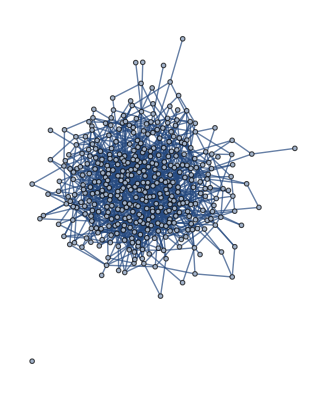

```mathematica
RandomGraph[{400,1000}]
```

```mathematica
FindClique[RandomGraph[{400,1000}]]
```

{{116,179,301}}

```mathematica
Names["*Dominat*"]
```

{DominatorTreeGraph,DominatorVertexList}

```mathematica
FindEdgeColoring[RandomGraph[{200,400}]]
```

{1,1,4,7,1,2,7,3,3,6,1,2,1,3,2,8,3,1,10,2,5,2,6,3,2,7,2,3,4,5,1,7,2,3,1,4,1,2,7,2,4,1,1,3,6,2,2,3,5,1,4,3,7,6,2,5,1,4,6,1,4,3,7,5,2,7,8,1,3,2,2,5,1,7,4,3,6,4,1,1,2,1,4,3,6,4,3,1,5,9,7,3,1,4,2,9,6,5,2,4,5,6,1,5,1,2,4,6,3,1,8,2,4,3,6,3,1,2,4,1,4,3,6,8,4,7,3,1,2,5,4,1,6,3,1,4,3,2,1,2,4,1,5,5,2,2,5,3,4,6,7,5,1,2,3,2,8,1,5,4,5,2,6,2,5,3,3,4,3,2,7,4,1,2,6,7,4,1,4,2,1,7,1,6,9,4,3,5,6,4,3,3,4,2,4,1,5,3,3,1,2,7,1,8,2,7,3,1,2,1,5,3,1,8,2,1,5,1,2,5,4,4,1,3,2,5,6,6,1,5,4,3,5,7,9,8,2,6,1,3,3,5,6,2,6,3,1,5,2,4,2,1,4,3,5,1,9,8,10,11,6,2,1,2,1,4,3,5,3,4,3,1,5,4,7,4,8,1,7,4,5,6,3,7,7,5,4,6,2,3,6,2,3,1,3,1,2,3,1,4,7,6,1,9,11,4,2,5,12,6,1,6,2,3,5,2,4,2,1,2,7,9,3,5,4,1,8,2,5,1,7,4,7,7,3,4,3,1,2,2,1,6,3,5,4,2,5,7,9,4,5,8,1,3,1,1,3,2,1,3,7,3,8,7,1,6,5,4,4,2,4,2,6,8,1,3,6,3,6,2,2,1,2,2,2,6,2,5,3,3,6,3,1,1,1,1,2,1,6,2}

```mathematica
FindVertexColoring[RandomGraph[{200,400}]]
```

{1,1,1,2,1,1,2,2,3,2,2,2,3,3,2,2,1,2,2,2,3,3,2,3,2,2,2,2,3,1,1,2,3,1,1,1,3,2,1,2,2,2,1,2,1,2,2,2,1,2,1,1,2,2,3,3,3,1,2,1,1,1,1,1,1,1,2,2,1,3,1,2,2,3,3,3,1,3,3,1,1,3,3,1,1,1,1,1,1,1,1,1,2,2,1,1,3,1,1,2,2,1,2,2,1,1,1,3,3,1,3,2,3,1,1,1,2,2,2,2,1,1,1,3,1,3,3,2,2,2,2,1,2,2,3,1,2,1,1,1,3,3,1,3,3,2,2,1,1,3,1,3,3,3,3,2,2,3,1,2,1,3,1,1,1,2,3,1,1,1,1,1,2,3,3,1,2,3,3,3,3,2,3,1,1,3,3,1,2,2,2,1,2,3,2,1,2,2,2,1}

```mathematica
g=CompleteGraph[3,3]
edgeWeights={{53,96,37},{47,87,41},{60,92,36}};
```

```mathematica
Flatten[edgeWeights]
```

{53,96,37,47,87,41,60,92,36}

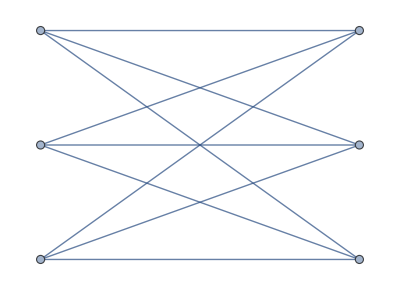

```mathematica
CompleteGraph[{3,3}]
```

```mathematica
EdgeList[CompleteGraph[{3,3}]]
```

{1<->4,1<->5,1<->6,2<->4,2<->5,2<->6,3<->4,3<->5,3<->6}

```mathematica
bipartiteGraph=CompleteGraph[{3,3},EdgeWeight->Thread[EdgeList[CompleteGraph[{3,3}]]->-{53,96,37,47,87,41,60,92,36}]]
```

-Graphics-

```mathematica
FindIndependentEdgeSet[bipartiteGraph]
```

{1<->6,2<->4,3<->5}

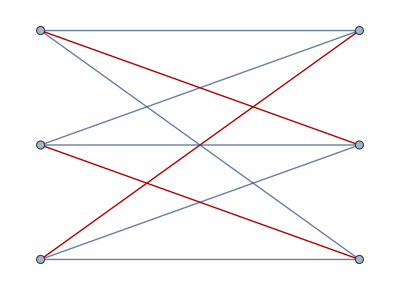

```mathematica
HighlightGraph[bipartiteGraph,FindIndependentEdgeSet[bipartiteGraph]]
```

```mathematica
AnnotationValue[{bipartiteGraph,FindIndependentEdgeSet[bipartiteGraph]},EdgeWeight]
```

{-37,-47,-92}

```mathematica
Total[AnnotationValue[{bipartiteGraph,FindIndependentEdgeSet[bipartiteGraph]},EdgeWeight]]
```

-176

```mathematica
Abs[Total[AnnotationValue[{bipartiteGraph,FindIndependentEdgeSet[bipartiteGraph]},EdgeWeight]]]
```

176

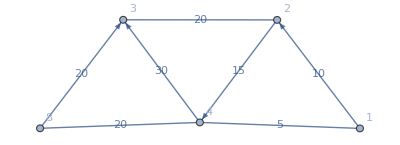

```mathematica
YouTubeGraph=Graph[{Annotation[1->2,EdgeWeight->10],Annotation[2<->3,EdgeWeight->20],Annotation[8->3,EdgeWeight->20],Annotation[1<->4,EdgeWeight->5],Annotation[2->4,EdgeWeight->15],Annotation[4<->8,EdgeWeight->20],Annotation[4->3,EdgeWeight->30]},EdgeLabels->"EdgeWeight",VertexLabels->Automatic]
```

```mathematica
ConnectedGraphQ[YouTubeGraph]
```

True

```mathematica
FindIndependentEdgeSet[YouTubeGraph]
```

FindIndependentEdgeSet[-Graphics-]

```mathematica
VertexList[YouTubeGraph,x_/;OddQ[VertexDegree[YouTubeGraph,x]]]
```

{2,3}

```mathematica
Subsets[EdgeList[YouTubeGraph]]
```

{{},{1->2},{2<->3},{8->3},{1<->4},{2->4},{4<->8},{4->3},{1->2,2<->3},{1->2,8->3},{1->2,1<->4},{1->2,2->4},{1->2,4<->8},{1->2,4->3},{2<->3,8->3},{2<->3,1<->4},{2<->3,2->4},{2<->3,4<->8},{2<->3,4->3},{8->3,1<->4},{8->3,2->4},{8->3,4<->8},{8->3,4->3},{1<->4,2->4},{1<->4,4<->8},{1<->4,4->3},{2->4,4<->8},{2->4,4->3},{4<->8,4->3},{1->2,2<->3,8->3},{1->2,2<->3,1<->4},{1->2,2<->3,2->4},{1->2,2<->3,4<->8},{1->2,2<->3,4->3},{1->2,8->3,1<->4},{1->2,8->3,2->4},{1->2,8->3,4<->8},{1->2,8->3,4->3},{1->2,1<->4,2->4},{1->2,1<->4,4<->8},{1->2,1<->4,4->3},{1->2,2->4,4<->8},{1->2,2->4,4->3},{1->2,4<->8,4->3},{2<->3,8->3,1<->4},{2<->3,8->3,2->4},{2<->3,8->3,4<->8},{2<->3,8->3,4->3},{2<->3,1<->4,2->4},{2<->3,1<->4,4<->8},{2<->3,1<->4,4->3},{2<->3,2->4,4<->8},{2<->3,2->4,4->3},{2<->3,4<->8,4->3},{8->3,1<->4,2->4},{8->3,1<->4,4<->8},{8->3,1<->4,4->3},{8->3,2->4,4<->8},{8->3,2->4,4->3},{8->3,4<->8,4->3},{1<->4,2->4,4<->8},{1<->4,2->4,4->3},{1<->4,4<->8,4->3},{2->4,4<->8,4->3},{1->2,2<->3,8->3,1<->4},{1->2,2<->3,8->3,2->4},{1->2,2<->3,8->3,4<->8},{1->2,2<->3,8->3,4->3},{1->2,2<->3,1<->4,2->4},{1->2,2<->3,1<->4,4<->8},{1->2,2<->3,1<->4,4->3},{1->2,2<->3,2->4,4<->8},{1->2,2<->3,2->4,4->3},{1->2,2<->3,4<->8,4->3},{1->2,8->3,1<->4,2->4},{1->2,8->3,1<->4,4<->8},{1->2,8->3,1<->4,4->3},{1->2,8->3,2->4,4<->8},{1->2,8->3,2->4,4->3},{1->2,8->3,4<->8,4->3},{1->2,1<->4,2->4,4<->8},{1->2,1<->4,2->4,4->3},{1->2,1<->4,4<->8,4->3},{1->2,2->4,4<->8,4->3},{2<->3,8->3,1<->4,2->4},{2<->3,8->3,1<->4,4<->8},{2<->3,8->3,1<->4,4->3},{2<->3,8->3,2->4,4<->8},{2<->3,8->3,2->4,4->3},{2<->3,8->3,4<->8,4->3},{2<->3,1<->4,2->4,4<->8},{2<->3,1<->4,2->4,4->3},{2<->3,1<->4,4<->8,4->3},{2<->3,2->4,4<->8,4->3},{8->3,1<->4,2->4,4<->8},{8->3,1<->4,2->4,4->3},{8->3,1<->4,4<->8,4->3},{8->3,2->4,4<->8,4->3},{1<->4,2->4,4<->8,4->3},{1->2,2<->3,8->3,1<->4,2->4},{1->2,2<->3,8->3,1<->4,4<->8},{1->2,2<->3,8->3,1<->4,4->3},{1->2,2<->3,8->3,2->4,4<->8},{1->2,2<->3,8->3,2->4,4->3},{1->2,2<->3,8->3,4<->8,4->3},{1->2,2<->3,1<->4,2->4,4<->8},{1->2,2<->3,1<->4,2->4,4->3},{1->2,2<->3,1<->4,4<->8,4->3},{1->2,2<->3,2->4,4<->8,4->3},{1->2,8->3,1<->4,2->4,4<->8},{1->2,8->3,1<->4,2->4,4->3},{1->2,8->3,1<->4,4<->8,4->3},{1->2,8->3,2->4,4<->8,4->3},{1->2,1<->4,2->4,4<->8,4->3},{2<->3,8->3,1<->4,2->4,4<->8},{2<->3,8->3,1<->4,2->4,4->3},{2<->3,8->3,1<->4,4<->8,4->3},{2<->3,8->3,2->4,4<->8,4->3},{2<->3,1<->4,2->4,4<->8,4->3},{8->3,1<->4,2->4,4<->8,4->3},{1->2,2<->3,8->3,1<->4,2->4,4<->8},{1->2,2<->3,8->3,1<->4,2->4,4->3},{1->2,2<->3,8->3,1<->4,4<->8,4->3},{1->2,2<->3,8->3,2->4,4<->8,4->3},{1->2,2<->3,1<->4,2->4,4<->8,4->3},{1->2,8->3,1<->4,2->4,4<->8,4->3},{2<->3,8->3,1<->4,2->4,4<->8,4->3},{1->2,2<->3,8->3,1<->4,2->4,4<->8,4->3}}

```mathematica
Select[Subsets[EdgeList[YouTubeGraph]],IndependentEdgeSetQ[YouTubeGraph,#]&]
```

{{},{1->2},{2<->3},{8->3},{1<->4},{2->4},{4<->8},{4->3},{1->2,8->3},{1->2,4<->8},{1->2,4->3},{2<->3,1<->4},{2<->3,4<->8},{8->3,1<->4},{8->3,2->4}}

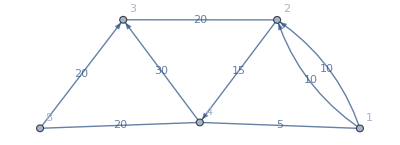
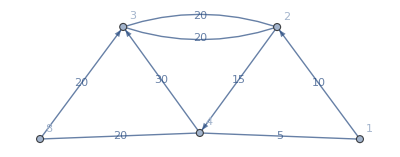
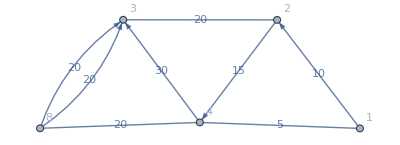
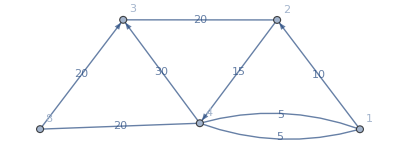
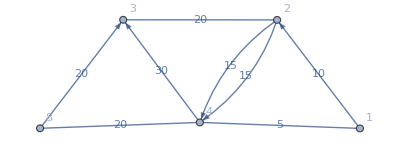
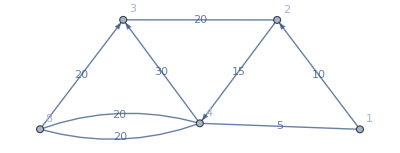
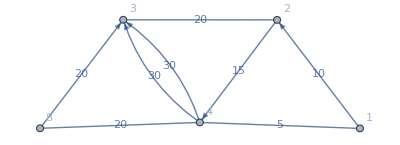
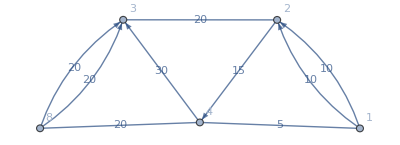
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
EdgeAdd[YouTubeGraph,#]&/@Select[Subsets[EdgeList[YouTubeGraph]],IndependentEdgeSetQ[YouTubeGraph,#]&]
```

```mathematica
MixedEulerianGraphQ[EdgeAdd[YouTubeGraph,#]]&/@Select[Subsets[EdgeList[YouTubeGraph]],IndependentEdgeSetQ[YouTubeGraph,#]&]
```

{False,False,True,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
ResourceFunctionDefinitionViewer["MixedEulerianGraphQ"]
```

```mathematica
Select[MixedEulerianGraphQ][EdgeAdd[YouTubeGraph,#]&/@Select[Subsets[EdgeList[YouTubeGraph]],IndependentEdgeSetQ[YouTubeGraph,#]&]]
```

{-Graphics-}